```mathematica
nPoly = 3; (*Highest Hermite polynomial to be used for ReLU approximation*)


(*ReLU and its approximation with Hermite polynomials*)
ReLU[x_]:= Max[0,x];
```

```mathematica
c[n_]:= Integrate[ t*HermiteH[n,t]*Exp[-t^2], {t,0,+Infinity}]/Sqrt[Sqrt[π]*2^n*Factorial[n]];
```

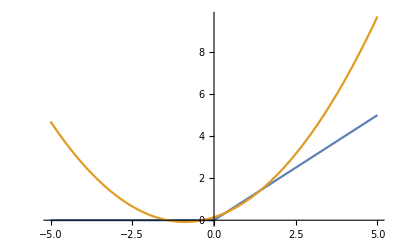

```mathematica
ApproxReLU[n_,x_]:=Expand[Sum[c[i]*HermiteH[i,x]/Sqrt[Sqrt[π]2^i*Factorial[i]],{i,0,n}]];
σ[y_] = ApproxReLU[nPoly,y]; (*Activation*)
Plot[{ReLU[x],σ[x]}, {x,-5.,5.}]
```

1/2+y/(√π)

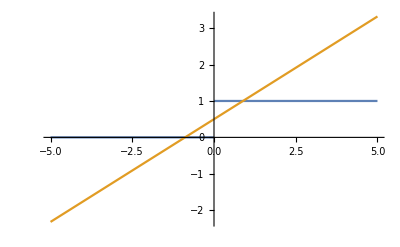

```mathematica
Derσ[y_]=D[σ[y],y]
Plot[{HeavisideTheta[x],Derσ[x]}, {x,-5.,5.}]
```

```mathematica
(*
	This a re actual calculation of all term needed.
	Convetions:
	  - lf[1] and lf[2] will be the local fields of the target, with activation		
*)
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

Get::noopen: Cannot open /Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m.

$Failed

```mathematica
target=lf[1] + lf[1]*lf[2];
```

lf[1]+lf[1] lf[2]

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[1]*target]
```

lf[1]^2/2+1/2 lf[1]^2 lf[2]+(lf[1]^2 lf[3])/(√π)+(lf[1]^2 lf[2] lf[3])/(√π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[2]*target]
```

1/2 lf[1] lf[2]+1/2 lf[1] lf[2]^2+(lf[1] lf[2] lf[3])/(√π)+(lf[1] lf[2]^2 lf[3])/(√π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[1]*σ[lf[4]]]
```

lf[1]/(8 √π)+(lf[1] lf[3])/(4 π)+1/4 lf[1] lf[4]+(lf[1] lf[3] lf[4])/(2 √π)+(lf[1] lf[4]^2)/(4 √π)+(lf[1] lf[3] lf[4]^2)/(2 π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[2]*σ[lf[4]]]
```

lf[2]/(8 √π)+(lf[2] lf[3])/(4 π)+1/4 lf[2] lf[4]+(lf[2] lf[3] lf[4])/(2 √π)+(lf[2] lf[4]^2)/(4 √π)+(lf[2] lf[3] lf[4]^2)/(2 π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[4]*target[lf[1],lf[2]]]
```

1/2 lf[4] (lf[1]+lf[1] lf[2])[lf[1],lf[2]]+(lf[3] lf[4] (lf[1]+lf[1] lf[2])[lf[1],lf[2]])/(√π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[4]*σ[lf[5]]]
```

lf[4]/(8 √π)+(lf[3] lf[4])/(4 π)+1/4 lf[4] lf[5]+(lf[3] lf[4] lf[5])/(2 √π)+(lf[4] lf[5]^2)/(4 √π)+(lf[3] lf[4] lf[5]^2)/(2 π)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*σ[lf[5]]*σ[lf[6]]]
```

1/(64 π)+lf[3]/(32 π^(3/2))+lf[4]/(32 π^(3/2))+(lf[3] lf[4])/(16 π^2)+lf[5]/(32 √π)+(lf[3] lf[5])/(16 π)+(lf[4] lf[5])/(16 π)+(lf[3] lf[4] lf[5])/(8 π^(3/2))+lf[5]^2/(32 π)+(lf[3] lf[5]^2)/(16 π^(3/2))+(lf[4] lf[5]^2)/(16 π^(3/2))+(lf[3] lf[4] lf[5]^2)/(8 π^2)+lf[6]/(32 √π)+(lf[3] lf[6])/(16 π)+(lf[4] lf[6])/(16 π)+(lf[3] lf[4] lf[6])/(8 π^(3/2))+1/16 lf[5] lf[6]+(lf[3] lf[5] lf[6])/(8 √π)+(lf[4] lf[5] lf[6])/(8 √π)+(lf[3] lf[4] lf[5] lf[6])/(4 π)+(lf[5]^2 lf[6])/(16 √π)+(lf[3] lf[5]^2 lf[6])/(8 π)+(lf[4] lf[5]^2 lf[6])/(8 π)+(lf[3] lf[4] lf[5]^2 lf[6])/(4 π^(3/2))+lf[6]^2/(32 π)+(lf[3] lf[6]^2)/(16 π^(3/2))+(lf[4] lf[6]^2)/(16 π^(3/2))+(lf[3] lf[4] lf[6]^2)/(8 π^2)+(lf[5] lf[6]^2)/(16 √π)+(lf[3] lf[5] lf[6]^2)/(8 π)+(lf[4] lf[5] lf[6]^2)/(8 π)+(lf[3] lf[4] lf[5] lf[6]^2)/(4 π^(3/2))+(lf[5]^2 lf[6]^2)/(16 π)+(lf[3] lf[5]^2 lf[6]^2)/(8 π^(3/2))+(lf[4] lf[5]^2 lf[6]^2)/(8 π^(3/2))+(lf[3] lf[4] lf[5]^2 lf[6]^2)/(4 π^2)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*σ[lf[5]]*target]
```

lf[1]/(16 √π)+(lf[1] lf[2])/(16 √π)+(lf[1] lf[3])/(8 π)+(lf[1] lf[2] lf[3])/(8 π)+(lf[1] lf[4])/(8 π)+(lf[1] lf[2] lf[4])/(8 π)+(lf[1] lf[3] lf[4])/(4 π^(3/2))+(lf[1] lf[2] lf[3] lf[4])/(4 π^(3/2))+1/8 lf[1] lf[5]+1/8 lf[1] lf[2] lf[5]+(lf[1] lf[3] lf[5])/(4 √π)+(lf[1] lf[2] lf[3] lf[5])/(4 √π)+(lf[1] lf[4] lf[5])/(4 √π)+(lf[1] lf[2] lf[4] lf[5])/(4 √π)+(lf[1] lf[3] lf[4] lf[5])/(2 π)+(lf[1] lf[2] lf[3] lf[4] lf[5])/(2 π)+(lf[1] lf[5]^2)/(8 √π)+(lf[1] lf[2] lf[5]^2)/(8 √π)+(lf[1] lf[3] lf[5]^2)/(4 π)+(lf[1] lf[2] lf[3] lf[5]^2)/(4 π)+(lf[1] lf[4] lf[5]^2)/(4 π)+(lf[1] lf[2] lf[4] lf[5]^2)/(4 π)+(lf[1] lf[3] lf[4] lf[5]^2)/(2 π^(3/2))+(lf[1] lf[2] lf[3] lf[4] lf[5]^2)/(2 π^(3/2))

```mathematica
IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*target[lf[1],lf[2]]^2]
```

1/4 ((lf[1]+lf[1] lf[2])[lf[1],lf[2]])^2+(lf[3] ((lf[1]+lf[1] lf[2])[lf[1],lf[2]])^2)/(2 √π)+(lf[4] ((lf[1]+lf[1] lf[2])[lf[1],lf[2]])^2)/(2 √π)+(lf[3] lf[4] ((lf[1]+lf[1] lf[2])[lf[1],lf[2]])^2)/π

```mathematica
IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]]
```

1/4+lf[3]/(2 √π)+lf[4]/(2 √π)+(lf[3] lf[4])/π